```mathematica
SetDirectory[NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\shiyin\work\git\work\critical_region\LPA\fixpoint_v3\LPA_mub0_Tc\buffer

```mathematica
fpi=Flatten[Import["./fpi.dat"]];
mpi=Flatten[Import["./mPion.dat"]];
msigma=Flatten[Import["./mSigma.dat"]];
T=Flatten[Import["./TMeV.dat"]];
```

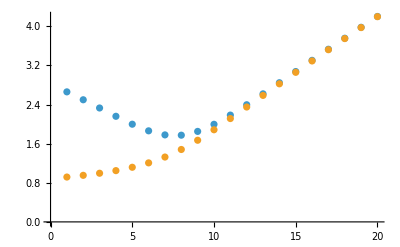

```mathematica
ListPlot[{msigma,mpi}]
```

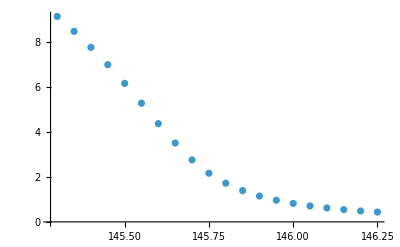

```mathematica
ListPlot[Transpose[{T,fpi}],PlotRange->All]
```